```mathematica
D[-1/4*Log[q[x]],x]
```

-q'[x]/(4 q[x])

```mathematica
D[-q'[x]/(4*q[x]),x]
```

q'[x]^2/(4 q[x]^2)-q''[x]/(4 q[x])

```mathematica
D[Sqrt[q[x]],x]
```

q'[x]/(2 √q[x])

```mathematica
Integrate[q''[x]/(2*q[x]^(3/2))+q'[x]/(2*q[x])-q'[x]^2/(2*q[x]^5/2),x]
```

∫(q'[x]/(2 q[x])-q'[x]^2/q[x]^5+q''[x]/(2 q[x]^(3/2)))ⅆx

```mathematica
D[q''[x]/(8*q[x]^(3/2))-5*q'[x]^2/(32*q[x]^(5/2)),x]
```

(25 q'[x]^3)/(64 q[x]^(7/2))-(q'[x] q''[x])/(2 q[x]^(5/2))+(q^(3)[x])/(8 q[x]^(3/2))

```mathematica
Integrate[9*q'[x]*q''[x]/(32*q[x]^3)-15*q'[x]^3/(64*q[x]^4)-q'''[x]/(16*q[x]^2),x]
```

(5 q'[x]^2)/(64 q[x]^3)-q''[x]/(16 q[x]^2)

```mathematica
sol=DSolve[{ϵ^2*y''[x]==(1+x^2)^2*y[x],y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→DifferentialRoot[Function[{y,x},{-(1+x^2)^2 y[x]+ϵ^2 y''[x]==0,y[0]==0,y'[0]==1}]][x]}}

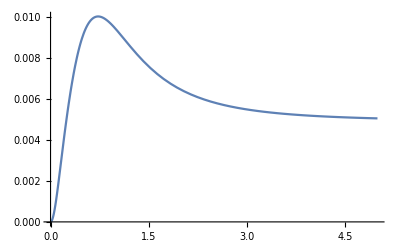

```mathematica
eru={ϵ->1/17};
Plot[(First[y[x]/.sol/.eru]-(ϵ/.eru)/Sqrt[1+x^2]*Sinh[1/(ϵ/.eru)*(x+x^3/3)])/First[y[x]/.sol/.eru],{x,0,5}]
```

```mathematica
eru={ϵ->2/35};
N@MaxValue[(First[y[x]/.sol/.eru]-(ϵ/.eru)/Sqrt[1+x^2]*Sinh[1/(ϵ/.eru)*(x+x^3/3)])/First[y[x]/.sol/.eru],x]
```

0.00975005

```mathematica
N@2/35
```

0.0571429

```mathematica
ClearAll[y1, y2,y1p, y2p, y1pp, y2pp,u1,u2,u1p,u2p]
```

```mathematica
y1[x_]:=q[x]^(-1/4)*Exp[1/ϵ*Integrate[Sqrt[q[r]],{r,s,x}]]
y1[x]
```

(ⅇ^((∫_s^x √q[r]ⅆr)/ϵ))/q[x]^(1/4)

```mathematica
y2[x_]:=q[x]^(-1/4)*Exp[-1/ϵ*Integrate[Sqrt[q[r]],{r,s,x}]]
y2[x]
```

(ⅇ^(-(∫_s^x √q[r]ⅆr)/ϵ))/q[x]^(1/4)

```mathematica
u1p[x_]:=Simplify[-y2[x]*f[x]*(1/ϵ^2)/(y1[x]*y2'[x]-y2[x]*y1'[x])]
u1p[x]
```

(ⅇ^(-(∫_s^x √q[r]ⅆr)/ϵ) f[x])/(2 ϵ q[x]^(1/4))

```mathematica
u2p[x_]:=Simplify[y1[x]*f[x]*(1/ϵ^2)/(y1[x]*y2'[x]-y2[x]*y1'[x])]
u2p[x]
```

-(ⅇ^((∫_s^x √q[r]ⅆr)/ϵ) f[x])/(2 ϵ q[x]^(1/4))

```mathematica
u1[x_]:=Integrate[u1p[s],{s,0,x}]
u1[x]
```

∫_0^x f[s]/(2 ϵ q[s]^(1/4))ⅆs

```mathematica
u2[x_]:=Integrate[u2p[s],{s,0,x}]
u2[x]
```

∫_0^x -f[s]/(2 ϵ q[s]^(1/4))ⅆs

```mathematica
u1[x]*y1[x]+u2[x]*y2[x]
```

(ⅇ^(-(∫_s^x √q[r]ⅆr)/ϵ) ∫_0^x -f[s]/(2 ϵ q[s]^(1/4))ⅆs)/q[x]^(1/4)+(ⅇ^((∫_s^x √q[r]ⅆr)/ϵ) ∫_0^x f[s]/(2 ϵ q[s]^(1/4))ⅆs)/q[x]^(1/4)

```mathematica
Integrate[(a*(x-x0)^β)^(1/2),x]
```

(2 (x-x0) √(a (x-x0)^β))/(2+β)

```mathematica
Integrate[-5*a^2/(32*(a*(x))^(5/2)),x]
```

(5 a^2 x)/(48 (a x)^(5/2))

```mathematica
q[x_]:=a*(x-x0)^β
```

```mathematica
Integrate[q''[x]/(8*q[x]^(3/2))-5*q'[x]^2/(32*q[x]^(5/2)),x]
```

(β (4+β))/(16 (x-x0) √(a (x-x0)^β) (2+β))

```mathematica
DSolve[{y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→Sin[x]}}

```mathematica
DSolve[{y''[x]+y[x]==-Sin[x]^3,y[0]==0,y'[0]==0},y[x],x]
```

{{y[x]→1/32 (12 x Cos[x]-8 Sin[x]^5-8 Cos[x] Sin[2 x]+Cos[x] Sin[4 x])}}